{4.94914,2.05086}

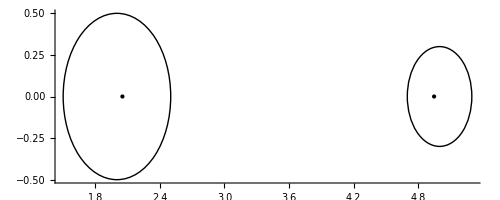

```mathematica
P = Eigenvalues[({{5, 0.3}, {-0.5, 2}})]
Graphics[{Circle[{5,0},0.3],Circle[{2,0},0.5],{PointSize[Large], Point[{P[[1]], 0}]}, {PointSize[Large], Point[{P[[2]], 0}]}}, Axes->True, AxesOrigin->{0,0}]
```

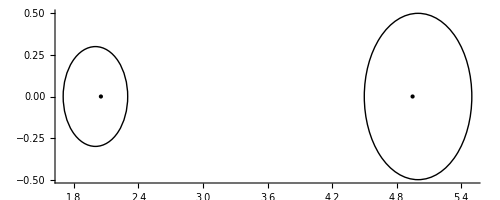

```mathematica
Graphics[{Circle[{5,0},0.5],Circle[{2,0},0.3],{PointSize[Large], Point[{P[[1]], 0}]}, {PointSize[Large], Point[{P[[2]], 0}]}}, Axes->True, AxesOrigin->{0,0}]
```

{2.99078,2.03731,0.971913}

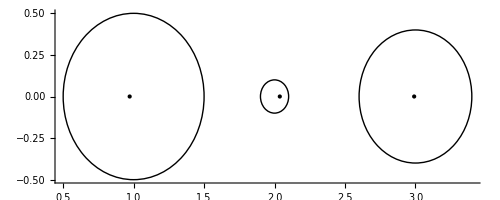

```mathematica
P = Eigenvalues[({{3, 0.2, -0.2}, {0, 2, 0.1}, {0.1, 0.4, 1}})]

Graphics[{Circle[{1,0},0.5],Circle[{2,0},0.1], Circle[{3,0},0.4], {PointSize[Large], Point[{P[[1]], 0}]}, {PointSize[Large], Point[{P[[2]], 0}]},  {PointSize[Large], Point[{P[[3]], 0}]}}, Axes->True, AxesOrigin->{0,0}]
```

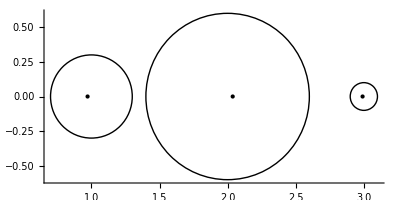

```mathematica
Graphics[{Circle[{1,0},0.3],Circle[{2,0},0.6], Circle[{3,0},0.1], {PointSize[Large], Point[{P[[1]], 0}]}, {PointSize[Large], Point[{P[[2]], 0}]},  {PointSize[Large], Point[{P[[3]], 0}]}}, Axes->True, AxesOrigin->{0,0}]
```

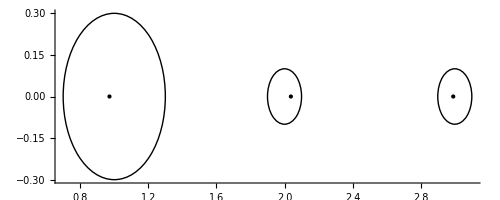

```mathematica
Graphics[{Circle[{1,0},0.3],Circle[{2,0},0.1], Circle[{3,0},0.1], {PointSize[Large], Point[{P[[1]], 0}]}, {PointSize[Large], Point[{P[[2]], 0}]},  {PointSize[Large], Point[{P[[3]], 0}]}}, Axes->True, AxesOrigin->{0,0}]
```

```mathematica
P = Eigenvalues[({{3, Cos[x], Cos[x]*Cos[x]}, {0, 5, Sin[x] * Sin[x]}, {3 Sin[x] * Sin[x], 3, 10}})]
```

{Root[-2298-6 Cos[x]-72 Cos[2 x]+9 Cos[3 x]-30 Cos[4 x]-3 Cos[5 x]+(1490+24 Cos[2 x]+6 Cos[4 x]) #1-288 #1^2+16 #1^3&,1],Root[-2298-6 Cos[x]-72 Cos[2 x]+9 Cos[3 x]-30 Cos[4 x]-3 Cos[5 x]+(1490+24 Cos[2 x]+6 Cos[4 x]) #1-288 #1^2+16 #1^3&,2],Root[-2298-6 Cos[x]-72 Cos[2 x]+9 Cos[3 x]-30 Cos[4 x]-3 Cos[5 x]+(1490+24 Cos[2 x]+6 Cos[4 x]) #1-288 #1^2+16 #1^3&,3]}

```mathematica
{Slider[Dynamic[t], {0,2Pi}],Dynamic[ 
Graphics[{ Red,Circle[{3,0},Abs[Cos[t] + Cos[t]^2]],Circle[{5,0},Abs[Sin[t]^2]], Circle[{10,0},Abs[3 + 3 Sin[t]^2]], Blue,Circle[{3,0},Abs[3 Sin[t]^2]],Circle[{5,0},Abs[3+ Cos[t] ]], Circle[{10,0},1]},  Axes->True, AxesOrigin->{0,0}, ImageSize->500] ]}
```

{,}

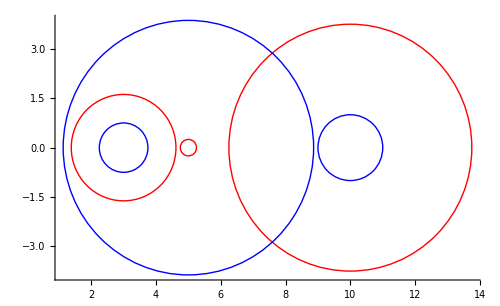

```mathematica
Graphics[{ Red,Circle[{3,0},Abs[Cos[x] + Cos[x]^2]],Circle[{5,0},Abs[Sin[x]^2]], Circle[{10,0},Abs[3 + 3 Sin[x]^2]], Blue,Circle[{3,0},Abs[3 Sin[x]^2]],Circle[{5,0},Abs[3+ Cos[x] ]], Circle[{10,0},1]},  Axes->True, AxesOrigin->{0,0}, ImageSize->500] /.{x->Pi/6}
```

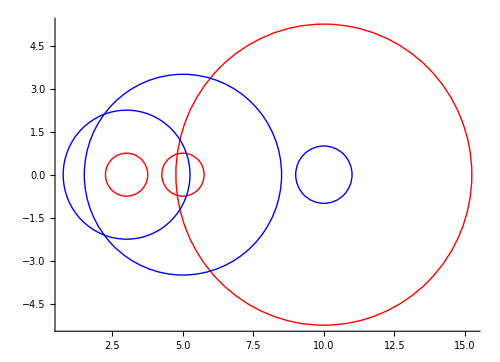

```mathematica
Graphics[{ Red,Circle[{3,0},Abs[Cos[x] + Cos[x]^2]],Circle[{5,0},Abs[Sin[x]^2]], Circle[{10,0},Abs[3 + 3 Sin[x]^2]], Blue,Circle[{3,0},Abs[3 Sin[x]^2]],Circle[{5,0},Abs[3+ Cos[x] ]], Circle[{10,0},1]},  Axes->True, AxesOrigin->{0,0}, ImageSize->500] /.{x->Pi/3}
```

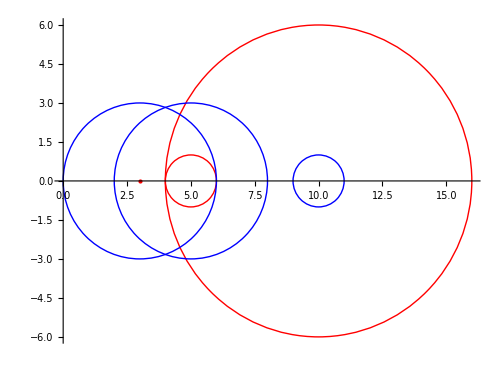

```mathematica
Graphics[{ Red,{PointSize[Large],Point[{3,0}]},Circle[{5,0},Abs[Sin[x]^2]], Circle[{10,0},Abs[3 + 3 Sin[x]^2]], Blue,Circle[{3,0},Abs[3 Sin[x]^2]],Circle[{5,0},Abs[3+ Cos[x] ]], Circle[{10,0},1]},  Axes->True, AxesOrigin->{0,0}, ImageSize->500] /.{x->Pi/2}
```